```mathematica
Quit
```

mutilde = input 

btilde = bInput/taap ==> bInput = taap * btilde

---- Check if M5μ makes any difference (Doest not seem so)

----- Check if everything is all right for the small B and small μ 

----- Check if things get better going to even larger ω

## M_XX, ξ_XX

### Importing (data,μB)

```mathematica
SetDirectory[NotebookDirectory[]<>"Chiral_conductivity"];

kZdata11=Get["corChiralγSUSYμT100d100B10000d10p6"];
kZdata12=Get["corChiralγSUSYμT100d100B250000d10p6"];
(*kZdata13=Get["corChiralγSUSYμT100d100B100000d10p6"];*)

kZdata21=Get["corChiralγSUSYμT1000d100B10000d10p6"];
kZdata22=Get["corChiralγSUSYμT1000d100B250000d10p6"];
(*kZdata23=Get["corChiralγSUSYμT1000d100B100000d10p6"];

kZdata11δμ=Get["corChiralγSUSYμT100d100ΔμB10000d10p6"];
kZdata12δμ=Get["corChiralγSUSYμT100d100ΔμB250000d10p6"];
kZdata13δμ=Get["corChiralγSUSYμT100d100ΔμB100000d10p6"];

kZdata21δμ=Get["corChiralγSUSYμT1000d100ΔμB10000d10p6"];
kZdata22δμ=Get["corChiralγSUSYμT1000d100ΔμB250000d10p6"];
kZdata23δμ=Get["corChiralγSUSYμT1000d100ΔμB100000d10p6"];*)

kZnumRN=Get["corChiralγSUSYμT10B10d10p6"];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"f_data"];

k0data11=Get["corrγSUSYμT1B1d100"];
k0data12=Get["corrγSUSYμT1B25d100"];
(*k0data13=Get["corrγSUSYμT1B1d10"];*)

k0data21=Get["corrγSUSYμT10B1d100"];
k0data22=Get["corrγSUSYμT10B25d100"];
(*k0data13=Get["corrγSUSYμT10B1d10"];

k0data11δμ=Get[""];
k0data12δμ=Get[""];
k0data13δμ=Get[""];

k0data21δμ=Get[""];
k0data22δμ=Get[""];
k0data13δμ=Get[""];*)


k0numRN=Get["corrγSUSYμT10B10d10p6"];
(* k0dataXXδμ is needed. *)
```

### Thermodynamics

```mathematica
γSub[data_]:=data⟦1,1⟧
bSub[data_]:=data⟦1,3⟧
μTSub[data_]:=data⟦1,2⟧
taap[data_]:=data⟦1,4⟧
entropy[data_]:=data⟦1,5⟧
w0[data_]:=data⟦1,6⟧+data⟦1,7⟧
kSub[data_]:=data⟦1,-1⟧

all[data_]:=data⟦2⟧

μSub[data_]:=μTSub[data]*taap[data]
ωgSize[data_]:=(data⟦2⟧//Dimensions)⟦1⟧
ωAxis[data_]:=(L+(1-Cos[(π #)/(2ωgSize[data]-1)])(U-L)&/@Range[0,ωgSize[data]-1])/.{L->10^-2,U->16π taap[data]}
```

#### Thermo data

```mathematica
μSub[#]&/@{k0numRN,kZnumRN,k0data11,k0data12,k0data21,k0data22,kZdata11,kZdata12,kZdata21,kZdata22}//N
bSub[#]&/@{k0numRN,kZnumRN,k0data11,k0data12,k0data21,k0data22,kZdata11,kZdata12,kZdata21,kZdata22}//N
taap[#]&/@{k0numRN,kZnumRN,k0data11,k0data12,k0data21,k0data22,kZdata11,kZdata12,kZdata21,kZdata22}//N
bSub[#]/taap[#]^2&/@{k0numRN,kZnumRN,k0data11,k0data12,k0data21,k0data22,kZdata11,kZdata12,kZdata21,kZdata22}//N
```

{1.68207,1.68207,0.313108,0.312342,1.68207,1.68245,0.313108,0.312342,1.68207,1.68245}

{0.00001,0.00001,0.01,0.25,0.01,0.25,0.01,0.25,0.01,0.25}

{0.168207,0.168207,0.313108,0.312342,0.168207,0.168245,0.313108,0.312342,0.168207,0.168245}

{0.000353436,0.000353436,0.102003,2.56258,0.353436,8.83198,0.102003,2.56258,0.353436,8.83198}

Probably the choice of Bt = 0.10 and 2.56 is best one. Take same for μT = 10 as well. 

For μT = 10, the background giving those two Bt are the following: 

“back090119γSUSYμT10B0p0029”    		B = 1443/500000 = 0.002886 		(was 0.1 for μT = 1)
“back090119γSUSYμT10B0p0725”             	B = 29/400 = 0.075 				(was 0.25 for μT = 1)

```mathematica
1443/500000.
%/(1/4)
```

0.002886

0.011544

```mathematica
29/400.
%/(1/10)
```

0.0725

0.725

### Kubo formula

Do we need to normalize M by their DC values?

#### M

```mathematica
M2X[data1_,data2_]:=-1/(2 bSub[data1]^2)(all[data1]⟦All, 5,6⟧-all[data2]⟦All, 5,6⟧)/kSub[data1]
M5X[data1_,data2_]:=-1/bSub[data1](all[data1]⟦All, 3,6⟧-all[data2]⟦All, 3,6⟧)/kSub[data1]
```

```mathematica
M2Y[data1_,data2_]:=-1/(2 bSub[data1]^2)(all[data1]⟦All, 5,6⟧)/kSub[data1]
```

#### M-derivative

```mathematica
M5μ[data1δ_,data2δ_,data1_,data2_]:=(M5X[data1δ,data2δ]-M5X[data1,data2])/Δμ/.Δμ->10^-10
```

Four data needed for M_5,μ

(μ, B)                            (μ, B = 0)

(μ + Δμ, B)                   (μ + Δμ, B = 0)

#### ξ

```mathematica
ξBX[data1_,data2_]:=1/(γSub[data1] μSub[data1])(all[data1]⟦All,1,2⟧-all[data2]⟦All,1,2⟧)/(ⅈ kSub[data1]) -1/3
ξVX[data1_,data2_]:=-2/(γSub[data1] μSub[data1]^2)(all[data1]⟦All,3,4⟧-all[data2]⟦All,3,4⟧)/(ⅈ kSub[data1]) 
ξTBX[data1_,data2_]:=-(all[data1]⟦All,3,2⟧-all[data2]⟦All,3,2⟧)/(ⅈ kSub[data1])
```

### Plot function

Module can be used to define function locally.

```mathematica
plotFunc[func_,data1_,data2_,ωLow_:1,ωHigh_:-1,pRangeLow_:1,pRangeHigh_:-1,dashing_:10]:=
Show[{
pFunc[Re,func,data1,data2,Red,dashing,ωLow,ωHigh,pRangeLow,pRangeHigh],
pFunc[Im,func,data1,data2,Blue,dashing,ωLow,ωHigh,pRangeLow,pRangeHigh]},

ImageSize->Medium,AxesLabel->{"ω/(2  π)",Subscript[#⟦1⟧, StringJoin[#⟦2;;-2⟧]]&@Characters[ToString[func]]},
PlotLabel->{"γ = 2/√3,  μ̃ = "<>ToString[N[μTSub[data1],2]]<>",  B̃ = "<>ToString[N[bSub[data1]/taap[data1]^2,2]]},
GridLines->Automatic] 


pFunc[ReIm_,func_,data1_,data2_,color_,dashing_,ωLow_:1,ωHigh_:-1,pRangeLow_:1,pRangeHigh_:-1]:=ListPlot[{ωAxis[data1]/(2π taap[data1]), ReIm[func[data1,data2]]}⟦All,ωLow;;ωHigh⟧//Transpose,Joined->True,InterpolationOrder->2,PlotStyle->{color,Dashing[dashing]},PlotRange->pRange[func,data1,data2,pRangeLow,pRangeHigh]]


pRange[func_,data1_,data2_,pRangeLow_:1,pRangeHigh_:-1]:=1.2{Min[Re[#],Im[#]],Max[Re[#],Im[#]]}&@func[data1,data2]⟦pRangeLow;;pRangeHigh⟧
```

### Plots

#### M_5

M_5 is independent of B. It only depends on μ. Thats why μ derivetive. 


To find the M_5 derivative, take a one set of data for each μ, preferably for smaller B.

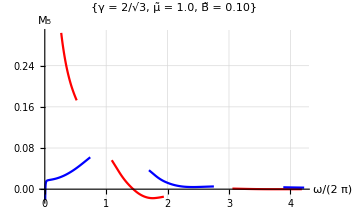
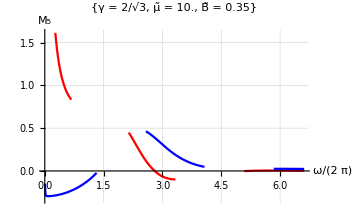

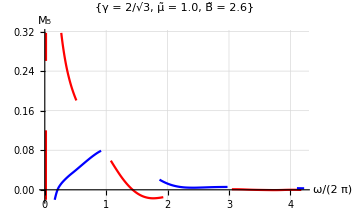
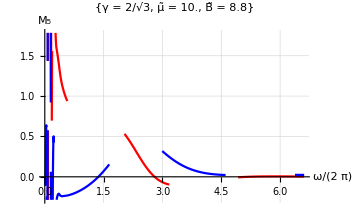

```mathematica
{plotFunc[M5X,kZdata11,k0data11,1,35,10,50],plotFunc[M5X,kZdata21,k0data21,1,45,10,50]}
{plotFunc[M5X,kZdata12,k0data12,1,35,10,50],plotFunc[M5X,kZdata22,k0data22,1,45,10,50]}
```

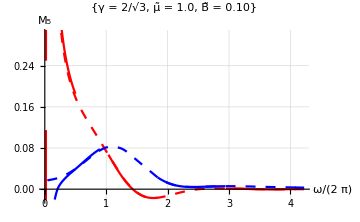
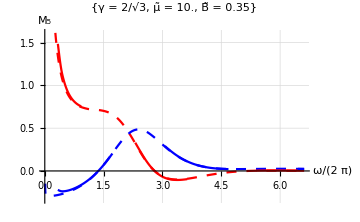

```mathematica
{Show[plotFunc[M5X,kZdata11,k0data11,1,35,10,50,0.02],plotFunc[M5X,kZdata12,k0data12,1,35,10,50]],
Show[plotFunc[M5X,kZdata21,k0data21,1,45,10,50,0.02],plotFunc[M5X,kZdata22,k0data22,10,45,10,50]]}
```

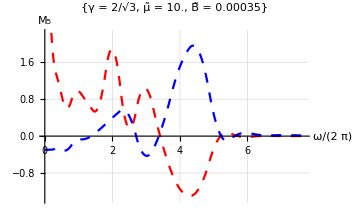

```mathematica
plotFunc[M5X,kZnumRN,k0numRN,1,20,10,20,0.02]
```

#### ξ_B

Look for the possibility to presenting same μ but different B data in the same plot

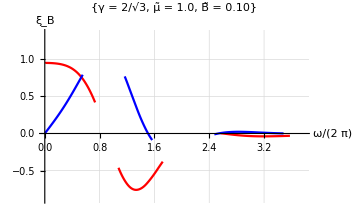
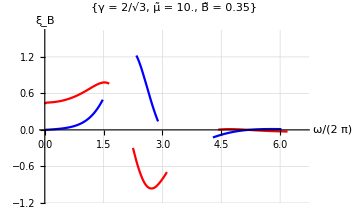

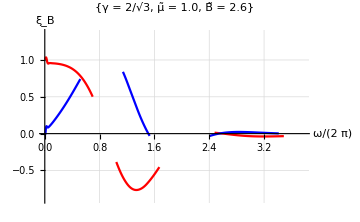
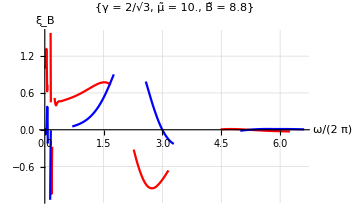

```mathematica
{plotFunc[ξBX,kZdata11,k0data11,1,33,10,50],plotFunc[ξBX,kZdata21,k0data21,1,45,10,50]}
{plotFunc[ξBX,kZdata12,k0data12,1,33,10,50],plotFunc[ξBX,kZdata22,k0data22,1,45,10,50]}
```

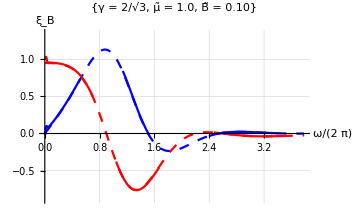
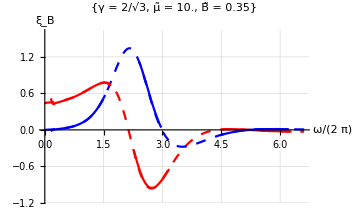

```mathematica
{Show[plotFunc[ξBX,kZdata11,k0data11,1,33,10,50,0.02],plotFunc[ξBX,kZdata12,k0data12,1,33,10,50]],Show[plotFunc[ξBX,kZdata21,k0data21,1,45,10,50,0.02],plotFunc[ξBX,kZdata22,k0data22,7,45,10,50]]}
```

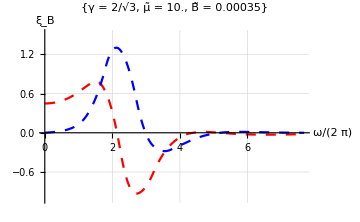

```mathematica
plotFunc[ξBX,kZnumRN,k0numRN,1,20,10,20,0.02]
```

Use the linear interpolation in the last plot. There can be continoius curve from w = 0 to w non zero.

#### ξ_V

Which is real and which is imaginary here?

Check RN limit here

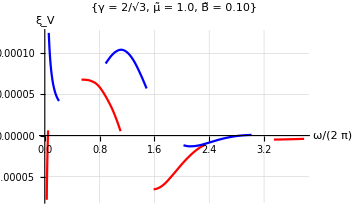
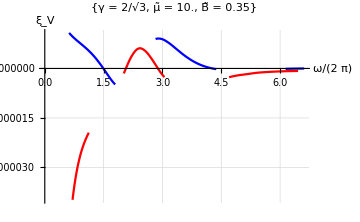

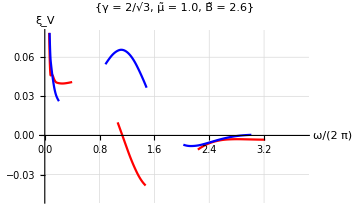
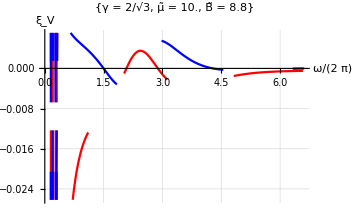

```mathematica
{plotFunc[ξVX,kZdata11,k0data11,1,33,10,50],plotFunc[ξVX,kZdata21,k0data21,1,45,15,50]}
{plotFunc[ξVX,kZdata12,k0data12,4,33,10,50],plotFunc[ξVX,kZdata22,k0data22,6,45,15,50]}
```

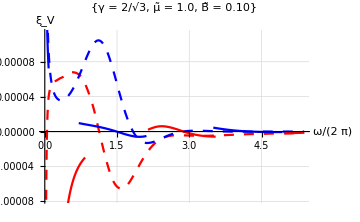
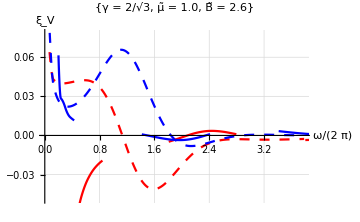

```mathematica
{Show[plotFunc[ξVX,kZdata11,k0data11,1,40,19,50,0.02],plotFunc[ξVX,kZdata21,k0data21,1,40,1,50]],
Show[plotFunc[ξVX,kZdata12,k0data12,5,33,10,50,0.02],plotFunc[ξVX,kZdata22,k0data22,7,50,8,50]]}
```

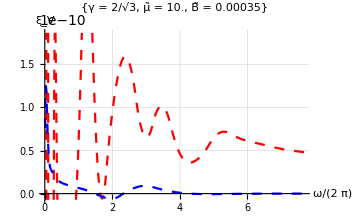

```mathematica
plotFunc[ξVX,kZnumRN,k0numRN,1,20,10,20,0.02]
```

If Bt is kept fixed, Would the curves look different?

The higher precision data is needed to see if the red curve going down in the last plot actially goes down. Linear interpolation can help in this case too.

#### M_2

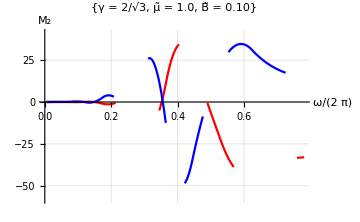
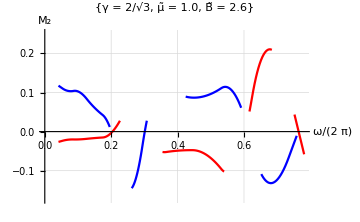

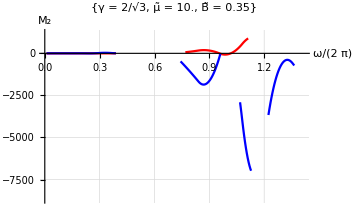
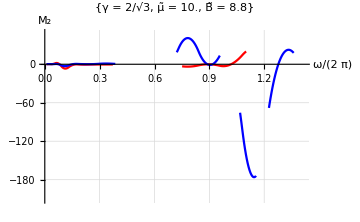

```mathematica
{plotFunc[M2X,kZdata11,k0data11,1,15,1,15],plotFunc[M2X,kZdata12,k0data12,4,15,1,15]}
{plotFunc[M2X,kZdata21,k0data21,1,20,1,20],plotFunc[M2X,kZdata22,k0data22,1,20,15,20]}
```

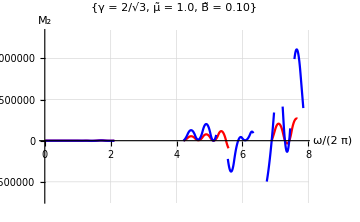
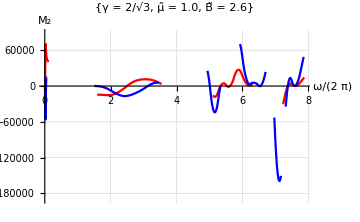

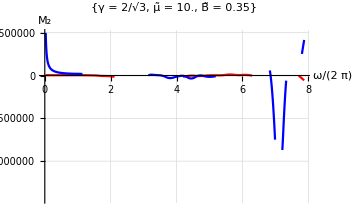
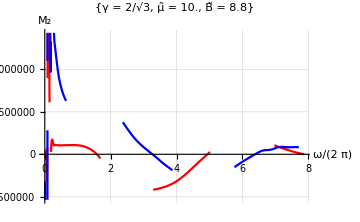

```mathematica
{plotFunc[M2Y,kZdata11,k0data11,1,50,1,50],plotFunc[M2Y,kZdata12,k0data12,1,50,1,50]}
{plotFunc[M2Y,kZdata21,k0data21,1,50,5,50],plotFunc[M2Y,kZdata22,k0data22,1,50,10,50]}
```

#### ξ_TB

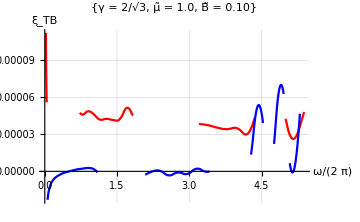
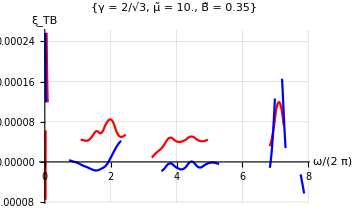

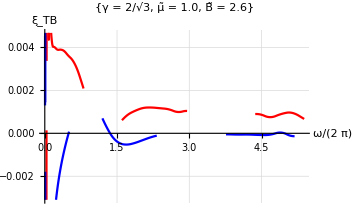
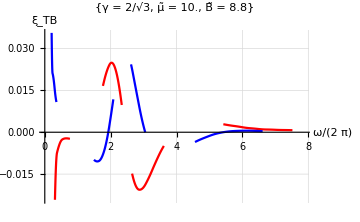

```mathematica
{plotFunc[ξTBX,kZdata11,k0data11,1,40,5,40],plotFunc[ξTBX,kZdata21,k0data21,1,50,10,50]}
{plotFunc[ξTBX,kZdata12,k0data12,1,40,9,50],plotFunc[ξTBX,kZdata22,k0data22,7,50,15,50]}
```

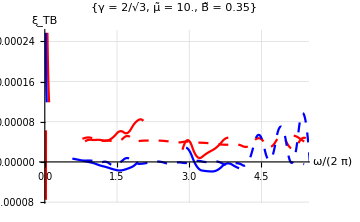
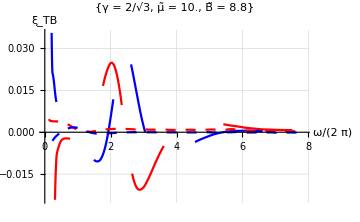

```mathematica
{Show[plotFunc[ξTBX,kZdata21,k0data21,1,40,9,50],plotFunc[ξTBX,kZdata11,k0data11,15,50,5,40,0.02]],Show[plotFunc[ξTBX,kZdata22,k0data22,7,50,15,50],plotFunc[ξTBX,kZdata12,k0data12,5,50,9,50,0.02]]}
```